# Data presentation and interpretation

Dr Vladimir Portnyk

Dr Daavid  Väänänen

I can understand only in human terms… I do not want to found anything on the incomprehensible. I want to know whether I can live with what I know and with that alone.-Graphics-

## Specification references 2.1 Interpret diagrams for single-variable data, including understanding that area in a histogram represents frequency Connect to probability distributions 2.2 Interpret scatter diagrams and regression lines for bivariate data, including recognition of scatter diagrams which include distinct sections of the population (calculations involving regression lines are excluded) Understand informal interpretation of correlation Understand that correlation does not imply causation 2.3 Interpret measures of central tendency and variation, extending to standard deviation Be able to calculate standard deviation, including from summary statistics 2.4 Recognise and interpret possible outliers in data sets and statistical diagrams Select or critique data presentation techniques in the context of a statistical problem Be able to clean data, including dealing with missing data, errors and outliers

Objectives:

¥	be able to calculate measures of location, mean, median and mode;
¥	be able to calculate measures of variation, standard deviation, variance, range and interpercentile range;
¥	be able to interpret and draw inferences from summary statistics.

The calculation of the mean, median and mode should be recapped from GCSE however the focus now is on students using Mathematica by Wolfram  to do the calculations. 

Be aware
When calculating the mean, of grouped data some student may divide by the number of groups rather than the number of items of data, they may also use class widths in the calculation rather than the mid-points.

Difficulties with coding are due to a lack of understanding about how coding affects the mean and standard deviation, and poor algebraic skills. Students sometimes substitute for the wrong variable, fail to solve equations correctly or get the order of operations the wrong way around.

Students should be reminded that they must be precise in their use of language.

Students should also remember to use accurate values throughout calculations to avoid losing marks due to premature rounding.

The data may be discrete or continuous, grouped or ungrouped, and students need to be able to interpret these summary statistics clearly and be able to make inferences from them. 

==Total[{25, 35, 10, 17, 29, 14, 21, 31}]
==Mean[{25, 35, 10, 17, 29, 14, 21, 31}]
==Median[{25, 35, 10, 17, 29, 14, 21, 31}]
==Dataset[AssociationThread[{“mean”, “median”, “sample standard deviation”}, N[Through[{Mean, Median, StandardDeviation}[{25, 35, 10, 17, 29, 14, 21, 31}]]]]]
==BoxWhiskerChart[{25, 35, 10, 17, 29, 14, 21, 31}]
==Histogram[{25, 35, 10, 17, 29, 14, 21, 31}, 5,Automatic]

https://www.wolframalpha.com/input/?i=mean%7B25,+35,+10,+17,+29,+14,+21,+31%7D

```mathematica
BoxWhiskerChart[{25, 35, 10, 17, 29, 14, 21, 31},BarOrigin->Left]
```

-Graphics-

TRUSTED TO DELIVER EXCELLENCE:  Hover over the bar to see min, max and more...

```mathematica
Median[{25, 35, 10, 17, 29, 14, 21, 31}]
```

23

```mathematica
StandardDeviation[{25, 35, 10, 17, 29, 14, 21, 31}]
```

5 √(43/14)

```mathematica
Dataset[AssociationThread[{"mean", "median", "sample standard deviation"}, N[Through[{Mean, Median, StandardDeviation}[{25, 35, 10, 17, 29, 14, 21, 31}]]]]]
```

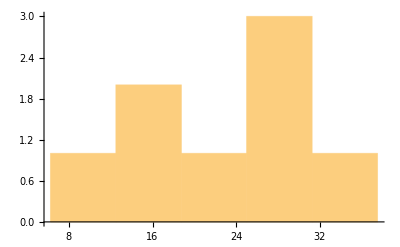

```mathematica
Histogram[{25, 35, 10, 17, 29, 14, 21, 31},{"Raw",5}]
```